# Neutral atoms/Rydberg qubits

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link if there is no such file found
Otherwise, use a locally-compiled that called quest_link*

```mathematica
(* Search for existing files that match the pattern "quest_link*" *)
With[{questLinkFiles=Sort@FileNames["quest_link*",{NotebookDirectory[]}]}
,
If[Length[questLinkFiles]>0,
(* If one or more matching files are found, use the first one alphabetically *)
Print["Using the existing link file: ",First@questLinkFiles];
CreateLocalQuESTEnv[First@questLinkFiles];
,
(*If no matching files are found, download the link file*)
Print["No link file found, download quest_link"];
CreateDownloadedQuESTEnv[];
];
]
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Get["../vqd.wl"]
```

## Set the default configuration of the netural atom device

frequency unit: MHz
time unit: μs
distance unit: μm (the VQD accepts 2 or 3 dimensional coordinates)

```mathematica
(* some examples of arrays *)
(* 2d-array of 9 atoms*)
locs2=Association@MapThread[#->#2&,{Range[0,8],Flatten[Table[{i,j},{i,0,2},{j,0,2}],1]}];
(* 3d-array of 8 atoms *)
locs3=Association@MapThread[#->#2&,{Range[0,7],Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2]}];
```

```mathematica
Options[RydbergHub]={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locs2
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 100*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 100*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 0.1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0.015, 01->0.025|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> Sqrt@2
,
(* blockade radius of each atom *)
BlockadeRadius -> 2
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 10
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.01
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 5*10^5
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 0.987
,
DurMeas -> 10
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0.05
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
```

## Elementary guide

### Native gates

Operators 
Initialisation and readout
Init_q, M_q

Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ], H_q, SRot_q[ϕ, Δ, dt] 

Two-qubit gates
CZ_(q1,q2)

Multi-qubit gates
C_(q1,q2,...)[Z_qt], C_qc[Z_(q1,q2,...)]

Register reconfiguration: swap the location of two atoms and shift the location of a bunch of atoms
SWAPLoc_(q1,q2), ShiftLoc_(q1,q2,...)

others: doing nothing
Wait_q[duration]

### The 2D- and 3D- dimensional arrays

```mathematica
device1=RydbergHub[];
```

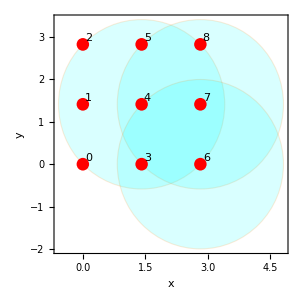

```mathematica
PlotAtoms[device1,ImageSize->300,BaseStyle->Directive[18,FontFamily->"Times"],ShowBlockade->{4,7,6}]
```

A 3D configuration. Here, we set the loss probability of measurement into 100%, thus, after measuring the atom is lost to the environment.
Set ShowLossAtoms to True to show the last position of the atoms before gone missing.

```mathematica
device2=RydbergHub[QubitNum->8,BlockadeRadius->1,UnitLattice->1,AtomLocations->locs3,ProbLossMeas->1];
InsertCircuitNoise[{Subscript[ShiftLoc, 5,7][{1,0,0}],Subscript[M, 5],Subscript[M, 7]},device2];
```

```mathematica
plot=PlotAtoms[device2,ImageSize->350,BaseStyle->Directive[14,FontFamily->"Times"],ShowBlockade->{0,4},ShowLossAtoms->True,LabelStyle->"Section"]
```

-Graphics3D-

```mathematica
(*Export["rydberg3d.pdf",Row@{Show[plot,ViewPoint->{1,-1.9,0}],Show[plot,ViewPoint->{0,-2,1.1}]}]*)
```

Initialisation will put back the atom to the tweezer at the initial configuration

```mathematica
InsertCircuitNoise[{Subscript[Init, 5],Subscript[Init, 7]},device2];
PlotAtoms[device2,ImageSize->300,BaseStyle->Directive[14,FontFamily->"Times"],ShowBlockade->{0,4},ShowLossAtoms->True]
```

-Graphics3D-

### Show the atoms and reconfiguring the register: PlotAtoms[]

Spatial locations accept 2D and 3D arrangements. Set  ShowBlockade → {qubits} to show the blockade radius.
Use command Options[function], to see what options that are available to a function. 
Also type ?function to see a short help about the function.

```mathematica
Options@PlotAtoms
```

{ShowBlockade→{},ShowLossAtoms→False}

Here we change the number of qubits, location, and the unit of lattice on the fly

```mathematica
locs=Association@MapThread[#->#2&,{Range[0,7],Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2]}]
```

<|0→{0,0,0},1→{0,0,1},2→{0,1,0},3→{0,1,1},4→{1,0,0},5→{1,0,1},6→{1,1,0},7→{1,1,1}|>

Atoms cannot be moved if place is occupied alread. Notice that the atoms moved experience enhance dephasing

```mathematica
dev3=RydbergHub[QubitNum->8,AtomLocations->locs,ProbLossMeas->1, UnitLattice->2.1];
InsertCircuitNoise[{Subscript[ShiftLoc, 1,7][{1,0,0}]},dev3]
```

InsertCircuitNoise::error: Encountered gate ShiftLoc_(1,7)[{1,0,0}] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

```mathematica
dev3=RydbergHub[QubitNum->8,AtomLocations->locs,ProbLossMeas->1, UnitLattice->2.1];
InsertCircuitNoise[{Subscript[ShiftLoc, 1,7][{-.5,.5,0}]},dev3]
```

{{0,{Depol_1[5.99998×10^-6],Deph_1[4.99998×10^-6],Depol_7[5.99998×10^-6],Deph_7[4.99998×10^-6]},{Depol_0[5.99998×10^-6],Deph_0[5.×10^-7],Depol_1[0.],Deph_1[0.],Depol_2[5.99998×10^-6],Deph_2[5.×10^-7],Depol_3[5.99998×10^-6],Deph_3[5.×10^-7],Depol_4[5.99998×10^-6],Deph_4[5.×10^-7],Depol_5[5.99998×10^-6],Deph_5[5.×10^-7],Depol_6[5.99998×10^-6],Deph_6[5.×10^-7],Depol_7[0.],Deph_7[0.]}},{100,{},{}}}

```mathematica
PlotAtoms[dev3]
```

-Graphics3D-

One can modify the plots using Graphics options

```mathematica
Options@PlotAtoms
```

{ShowBlockade→{},ShowLossAtoms→False}

```mathematica
Options@Graphics
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

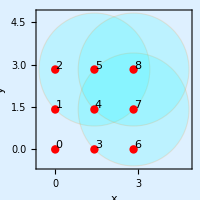

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{5,7,8},ImageSize->200,Background->LightBlue]
```

### Arbitrary single rotation

Hadamard: ϕ→0,Δ→Ω,t→π/Ω̃

Here, I assign Ω with the default value of RabiFreq for practicality. Then I check what matrix produced with SRot[] gate given value.
I access Aliases definition to replace SRot[] definition since it is not a native QuESTLink gate by replace command /.

```mathematica
Ω=OptionValue[RydbergHub,RabiFreq]
```

0.1

```mathematica
CalcCircuitMatrix[Subscript[SRot, 0][0,Ω,π/Sqrt[2 Ω^2]]/.RydbergHub[][Aliases]]//Chop//MatrixForm
```

(0.-0.707107 ⅈ | 0.-0.707107 ⅈ
0.-0.707107 ⅈ | 0.+0.707107 ⅈ)

Rotation around x-axis  via  SRot[ϕ→0,Δ→0,t→θ/Ω ] or directly using Rx[θ].

Chop[] is called to remove the thrilling zeros

```mathematica
CalcCircuitMatrix[Subscript[Rx, 0][π/Ω]]//MatrixForm
```

(-1.+0. ⅈ | 0.-6.12323×10^-16 ⅈ
0.-6.12323×10^-16 ⅈ | -1.+0. ⅈ)

```mathematica
CalcCircuitMatrix[Subscript[Rx, 0][π]]//Chop//MatrixForm
```

(0 | -ⅈ
-ⅈ | 0)

```mathematica
CalcCircuitMatrix[Subscript[SRot, 0][0,0,π/Ω]/.RydbergHub[][Aliases]]//Chop//MatrixForm
```

(0 | 0.-1. ⅈ
0.-1. ⅈ | 0)

### Multi-qubit gates must fulfill blockade requirement

The operation controlled-Z up to a single qubit phase ϕ : inside blockade vs outside blockade

```mathematica
CalcCircuitMatrix[Subscript[CZ, 0,1][ϕ]/.RydbergHub[][Aliases]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(ⅈ (-π+2 ϕ)))

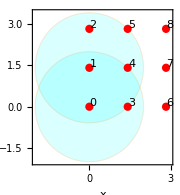

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},device1]
```

{{0,{CZ_(0,1)[ϕ],KrausNonTP_(0,1)[{{{1,0,0,0},{0,0.9995,0,0},{0,0,0.9995,0},{0,0,0,0.9995}}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[8.48225×10^-6],Deph_2[6.28318×10^-7],Depol_3[8.48225×10^-6],Deph_3[6.28318×10^-7],Depol_4[8.48225×10^-6],Deph_4[6.28318×10^-7],Depol_5[8.48225×10^-6],Deph_5[6.28318×10^-7],Depol_6[8.48225×10^-6],Deph_6[6.28318×10^-7],Depol_7[8.48225×10^-6],Deph_7[6.28318×10^-7],Depol_8[8.48225×10^-6],Deph_8[6.28318×10^-7]}},{125.664,{},{}}}

The device dev below has a more separated lattice. The atoms are not in the blockade radii, thus, CZ_(0,1)[ϕ] gate application becomes illegal and returns error.

```mathematica
dev=RydbergHub[UnitLattice->0.00001+2√2];
```

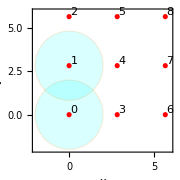

```mathematica
PlotAtoms[dev,ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},dev]
```

InsertCircuitNoise::error: Encountered gate CZ_(0,1)[ϕ] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

Multiqubit gates C_c__[Z_t__] or C_c__[Z_t__] , every qubit in cq and tq must be in each other in the blockade radius.
In the following example, qubits{ 0,1,3,4} , { 3,4,6,7}, {5,4,7,8 }have overlapping blockade radius; they must produce legit multi-qubit gates.
side note: Variable j_ accepts input with 1 entry. j__ accepts input with at least one entry

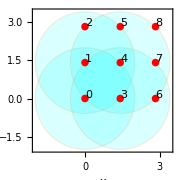

```mathematica
dev=RydbergHub[];
PlotAtoms[dev,ShowBlockade->{0,1,3,4},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[C, 4][Subscript[Z, 3,6,7]],Subscript[C, 4,5,7][Subscript[Z, 8]],Subscript[C, 2,5][Subscript[Z, 4]]},dev];
```

variable % is useful to pass the outcome of previous executed command

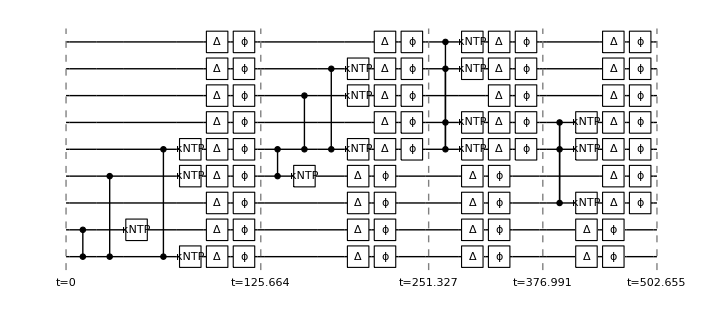

```mathematica
DrawCircuit@%
```

### Operations outside native gates and how to verify

We can define an arbitrary gates above this layer straightforwardly using ReplaceAll[]. For example, I will replace simple Toffoli (where the last qubit becomes the target) with Rydberg native multi-z gate and hadamard.

```mathematica
gateRule={Subscript[Toff, q__]:>With[{c=Sequence@@({q}[[;;-2]]),t=Last@{q}},{Subscript[H, t],Subscript[C, c][Subscript[Z, t]],Subscript[H, t]}]};
```

```mathematica
circ={Subscript[Toff, 0,1,2],Subscript[Toff, 2,3,4,5],Subscript[Toff, 0,1,2,3,4,5]};
DrawCircuit[%]
```

-Graphics-

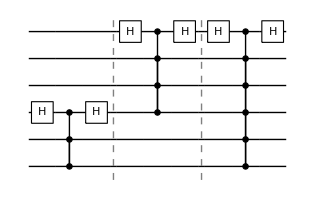

```mathematica
DrawCircuit[circ/.gateRule]
```

Note that, quest is using Least significant bit! so be careful with the indices!

For example, in the case of CNOT gate one commonly sees:
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)
that is because the indices  arranged from behind: {q0q1...qn}, e.g matrix above has basis  {00,01,10,11}. QuEST arrangement is {qn...q1q0}! Thus, instead, you will see

```mathematica
cnot=CalcCircuitMatrix[Subscript[C, 0][Subscript[X, 1]]];
```

```mathematica
cnot//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

For instance, here is my function to rearrange the matrix to looks like the commonly defined order

```mathematica
rearrange[mat_]:=With[{d=Length@mat,nq=Log2[Length@mat]},
Table[mat[[Sequence@@(1+{FromDigits[Reverse@IntegerDigits[r,2,nq],2],FromDigits[Reverse@IntegerDigits[c,2,nq],2]})]],{r,0,d-1},{c,0,d-1}]
]
```

```mathematica
rearrange[cnot]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Before rearrange

```mathematica
CalcCircuitMatrix[Subscript[Toff, 0,1,2,3]/.gateRule]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

After rearrange

```mathematica
CalcCircuitMatrix[Subscript[Toff, 0,1,2,3]/.gateRule]//rearrange//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

### Spatial operations

We can do consecutive commands. The instance dev will store previous state from the lass InsertCircuitNoise[] call.

```mathematica
dev=RydbergHub[];
```

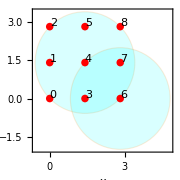

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 0,1,2][{0,0.5}],Subscript[SWAPLoc, 8,7],Subscript[Wait, 0][.1],Subscript[ShiftLoc, 7,8,6][{0,-0.5}],Subscript[SWAPLoc, 4,6]},dev];
```

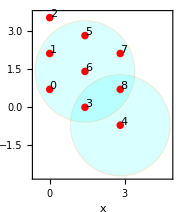

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 7,8,4][{0.5,0}]},dev];
```

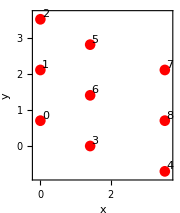

```mathematica
PlotAtoms[dev,ImageSize->Small]
```

### Scheduling : Rearrange circuit by parallel and serial

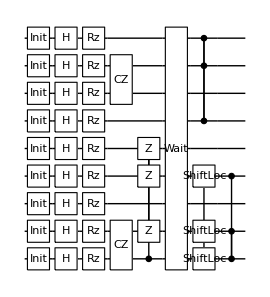

```mathematica
circ=Flatten@{{Subscript[Init, #],Subscript[H, #],Subscript[Rz, #][π/(#+1)]}&/@Range[0,8],Subscript[CZ, 6,7][π],Subscript[CZ, 0,1][π],Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[Wait, Range[0,8]][ϕ],Subscript[ShiftLoc, 0,1,3][{-1,0}],Subscript[C, 0,1][Subscript[Z, 3]],Subscript[C, 5,8][Subscript[Z, 7]]};
DrawCircuit@%
```

Parallel excution, where paralellism applies when the operations are done without non-overlaping blockade radius (future)
At the moment, it applies when it is not a multi-qubit gate. But initialisation is in parallel in nature.

```mathematica
Options@CircRydbergHub
```

{Parallel→False}

```mathematica
serialcirc=CircRydbergHub[circ,RydbergHub[]];
```

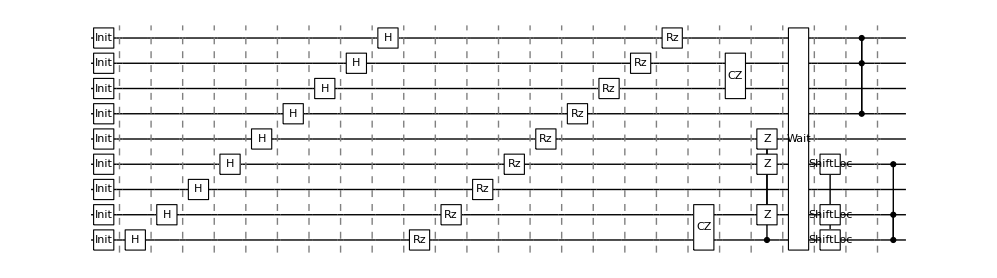

```mathematica
DrawCircuit@serialcirc
```

Serial excution. We rearrange a list of gates into a list of list {{... }, {...}, ... }.
The gates within the same inner list { ... } are executed in parallel. The schedule time is taken based on the maximal duration of the gates among the inner list.
One may edit this manually.

```mathematica
dev=RydbergHub[];
```

```mathematica
PlotAtoms[dev,ImageSize->Small,ShowBlockade->{0,1,3,4}]
```

-Graphics-

```mathematica
parallelcirc=CircRydbergHub[circ,dev,Parallel->True]
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},{H_0,H_1,H_2,H_3,H_4,H_5,H_6,H_7,H_8},{Rz_0[π],Rz_1[π/2],Rz_2[π/3],Rz_3[π/4],Rz_4[π/5],Rz_5[π/6],Rz_6[π/7],Rz_7[π/8],Rz_8[π/9]},{CZ_(6,7)[π]},{CZ_(0,1)[π]},{C_0[Z_(1,3,4)]},{Wait_{0,1,2,3,4,5,6,7,8}[ϕ]},{ShiftLoc_(0,1,3)[{-1,0}]},{C_(5,8)[Z_7]},{C_(0,1)[Z_3]}}

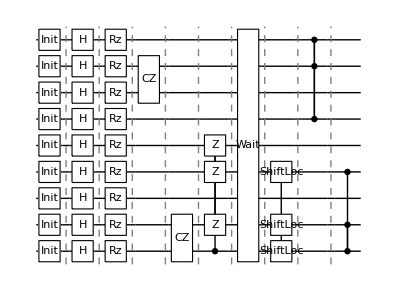

```mathematica
DrawCircuit@%
```

For example, I execute the hadamards in pair for some reason.

```mathematica
serialcirc2={{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8]},{Subscript[H, 0],Subscript[H, 1]},{Subscript[H, 2],Subscript[H, 3]},{Subscript[H, 4],Subscript[H, 5]},{Subscript[H, 6],Subscript[H, 7]},{Subscript[H, 8]},{Subscript[Rz, 0][π]},{Subscript[Rz, 1][π/2]},{Subscript[Rz, 2][π/3]},{Subscript[Rz, 3][π/4]},{Subscript[Rz, 4][π/5]},{Subscript[Rz, 5][π/6]},{Subscript[Rz, 6][π/7]},{Subscript[Rz, 7][π/8]},{Subscript[Rz, 8][π/9]},{Subscript[CZ, 0,1][π]},{Subscript[CZ, 6,7][π]},{Subscript[C, 0][Subscript[Z, 1,3,4]]},{Subscript[Wait, {0,1,2,3,4,5,6,7,8}][ϕ]},{Subscript[ShiftLoc, 0,1,3][{-1,0}]},{Subscript[C, 5,8][Subscript[Z, 7]]},{Subscript[C, 0,1][Subscript[Z, 3]]}};
```

Get noise-decorated circuit from rearranged circuit, where hadamard are run in pairs, in parallel

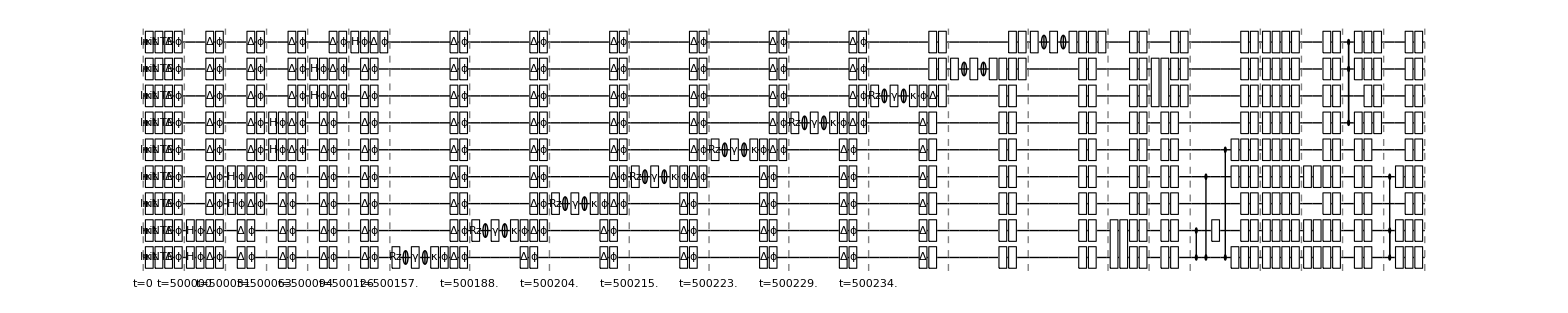

```mathematica
DrawCircuit@InsertCircuitNoise[serialcirc2,dev]
```

## Example: quantum simulationon creating 9-GHZ

```mathematica
ghz={
Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],
Subscript[H, 0],
Subscript[H, 1],Subscript[H, 3],Subscript[H, 4], Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[H, 1],Subscript[H, 3],Subscript[H, 4],
Subscript[H, 6],Subscript[H, 7],Subscript[C, 3][Subscript[Z, 6,7]],Subscript[H, 6],Subscript[H, 7],
Subscript[H, 5],Subscript[H, 8],Subscript[C, 7][Subscript[Z, 5,8]],Subscript[H, 5],Subscript[H, 8],
Subscript[H, 2],Subscript[C, 1][Subscript[Z, 2]],Subscript[H, 2]
};
```

```mathematica
(* allocate memory *)
ψ=CreateQureg[9];
ρ=CreateDensityQureg[9];
```

The non-native questlink gates are defined in the Aliases, so we need to replace those aliases into the native questlink gates. Apply the circuit in the state vector, noiseless case (note that we remove the damping here because it’s vector simulation)

```mathematica
ApplyCircuit[InitZeroState@ψ,Flatten[ghz/.dev[Aliases]/.{Subscript[Damp, q_][_]:>Subscript[Id, q]}]];
```

Initialise the qubits in a  random mixed state: extremely low fidelity. Note that CalcFidelity accepts density matrix and state vector. It cannot compare two density matrices.

```mathematica
SetQuregMatrix[ρ,RandomMixState[9]];
CalcFidelity[ρ,ψ]
```

0.00202768

Then apply the circuit in serial manner

```mathematica
dev=RydbergHub[];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[CircRydbergHub[ghz,dev,Parallel->False],dev,ReplaceAliases->True]];
```

```mathematica
CalcFidelity[ρ,ψ]
```

0.907664

## Paper Supplement

Here we replicate the experiment in : www.nature.com/articles/s41586-022-04592-6
See Graphstate1D.nb and Steane7.nb in  folder supplement/GraphStatesonRydbergHub for the complete simulation code

## 1D graph state generation

```mathematica
(* memory initialisation*)
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
```

### Plots

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

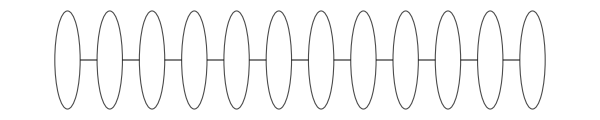

```mathematica
g=Graph[#<->#+1&/@Range[0,10]];
Graph[g,VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{13,FontFamily->"Serif"},ImageSize->600,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center]]
(*Export["~/vqd/img/graph1d.pdf",%]*)
```

#### Default device configuration

```mathematica
Options[RydbergHub]={
QubitNum-> 12,
AtomLocations->Association@Table[j->{j,0},{j,0,11}],
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.001, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.975,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.01,11->0.0001|>
};
```

#### Plots generation

```mathematica
ClearAll[showgs]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.96,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},None},{Automatic,None}}
];
```

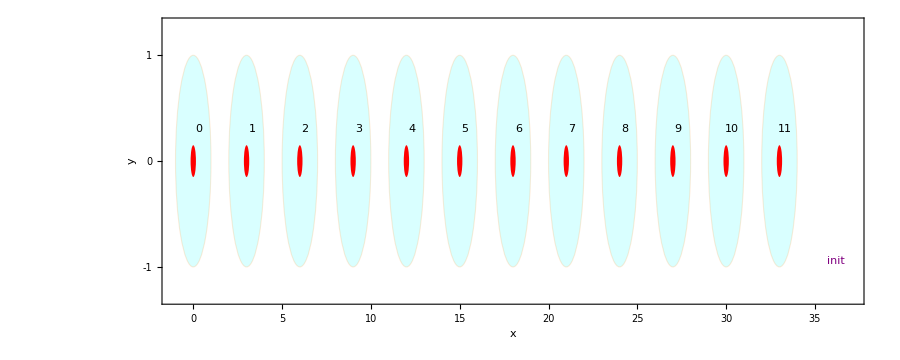

```mathematica
devGS=RydbergHub[];
showgs["init"]
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["move 1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["move 2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

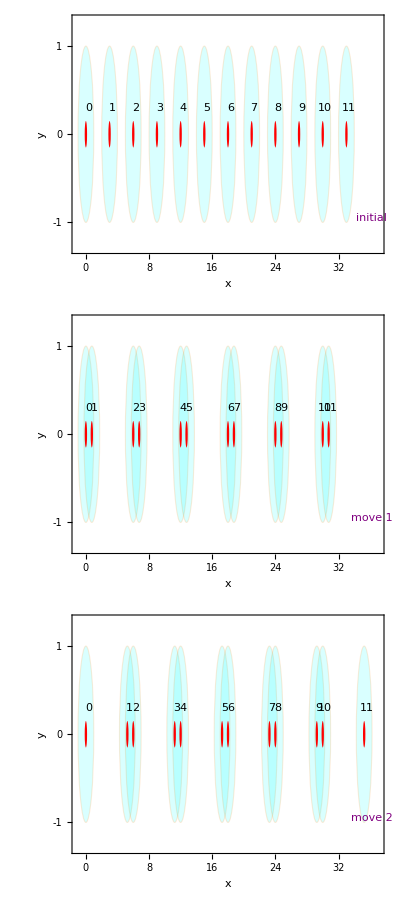

```mathematica
Column[{f1,f2,f3},Spacings->0]
(*Export["~/vqd/img/rydberg_graph.pdf",%]*)
```

### Results

#### Modules related to displaying the results

```mathematica
chartGraph1D[res_,expresults_]:=With[{scount=res["scount"],nshots=res["outeven"]//Length,stabideal=res["sideal"]},
Show[
BarChart[Values@scount/nshots,
ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),
Frame->True,FrameStyle->Directive[Black,Thick],
AspectRatio->1.2,
ChartStyle->ColorData["DeepSeaColors"][0.7],
PlotRange->{Automatic,{-0.05,1}}]
,
BarChart[expresults,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
,
ListPlot[stabideal,Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]]
,
ImageSize->{Automatic,400},Background->White,LabelStyle->{16,FontFamily->"Serif"},ImagePadding->{{30,5},{30,10}}
]
]

showResultGraph1D[res_,expresults_]:=With[
{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outeven"]//Length}
,
<|"nshots"->ToString@nshots,
"chart"->chartGraph1D[res,expresults],
"benchmark"->Table[Between[res[["scount"]][j-1]/nshots,Sort[expresults[[j]][[1]]+{1,-1}*expresults[[j]][[2]]]],{j,Length@expresults}],
"erravg"->Mean@Abs[N[Values@res[["scount"]]/nshots]-expresults],
"errmax"->Max@Abs[N[Values@res[["scount"]]/nshots]-First/@expresults],
"stabavg"->N@Mean@Values@res[["scount"]]/nshots,
"nospamavg"->Mean@res[["sideal"]]|>
]
```

#### Quoted from the paper to compare

-Graphics-

```mathematica
cs1dmean={0.8814814814814814,0.8314814814814814,0.8888888888888887,0.8629629629629629,0.8814814814814814,0.8796296296296295,0.8555555555555554,0.8759259259259258,0.8722222222222221,0.8777777777777775,0.8462962962962962,0.8925925925925925};
cs1dminus={0.8537037037037036,0.8018518518518518,0.8629629629629629,0.8333333333333333,0.8537037037037036,0.8537037037037036,0.8277777777777777,0.8481481481481481,0.8444444444444444,0.8481481481481481,0.8185185185185184,0.8685185185185184};
cs1dplus={0.9018518518518518,0.8574074074074074,0.912962962962963,0.8870370370370371,0.9037037037037035,0.9037037037037035,0.8814814814814814,0.898148148148148,0.8962962962962961,0.898148148148148,0.8722222222222221,0.9148148148148149};
```

```mathematica
cs1d=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{cs1dmean,cs1dminus,cs1dplus}]
```

{0.8810.0280.020,0.8310.0300.026,0.8890.0260.024,0.8630.0300.024,0.8810.0280.022,0.8800.0260.024,0.8560.0280.026,0.8760.0280.022,0.8720.0280.024,0.8780.0300.020,0.8460.0280.026,0.8930.0240.022}

#### Results from simulation

```mathematica
grahstate1d<<"supplement/GraphStatesonRydbergHub/graphstate1d.mx";
```

```mathematica
graphstate1d//Length
```

47

```mathematica
allres=showResultGraph1D[#,cs1d]&/@graphstate1d;
```

```mathematica
(* best results: 11/12 stabilizer measurements agree with the experimental results*)
Count[#,True]&/@allres[[All,"benchmark"]]
best=Flatten@Position[%,x_/;x>=11]
```

{7,8,8,7,8,6,3,8,9,11,9,6,7,7,6,8,7,11,6,4,8,4,5,8,9,9,8,8,6,6,7,8,8,9,10,8,9,8,8,10,8,7,10,8,9,9,10}

{10,18}

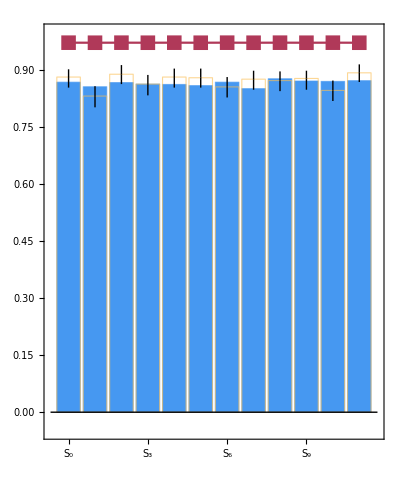
<|nshots→2000,chart→-Graphics-,benchmark→{True,True,True,True,True,True,True,False,True,True,True,True},erravg→0.0160.0080.007,errmax→0.0249259,stabavg→0.865333,nospamavg→0.971812|>

```mathematica
(* the result shown in the paper *)
showResultGraph1D[graphstate1d[[18]],cs1d]
```

```mathematica
(*Export["stab_gs.pdf",showResultGraph1D[graphstate1d[[18]],cs1d][["chart"]]]*)
```

## Steane code

#### Default device configuration

```mathematica
Options[RydbergHub]={
QubitNum-> 7,
AtomLocations-><|6->{0,1},5->{1,1},2->{2,1},1->{4,1},4->{2,0},0->{4,0},3->{5,0}|>,
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.001, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.975,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.01,11->0.0001|>
};
```

#### Plots generation

```mathematica
devst=RydbergHub[];
```

```mathematica
ClearAll[showst]
showst[title_:"",opt_:{}]:=PlotAtoms[devst,Sequence@@opt,ImageSize->600,ShowBlockade->Range[0,6],LabelStyle->Directive[Italic, 15,Black],BaseStyle->{17,FontFamily->"Serif"},PlotRange->{{-8,16},{-1.3,4.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.2,0.1}]],Frame->True,FrameStyle->Directive[Black,Thick],Axes->False];
```

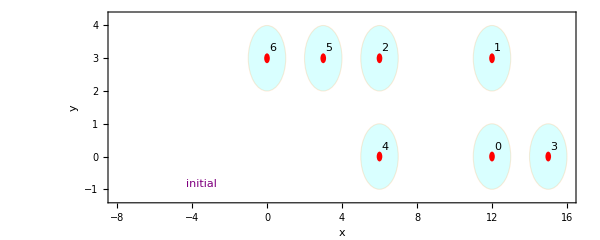

```mathematica
move0=showst["initial",{ImagePadding->{{20,18},{0,18}}}]
```

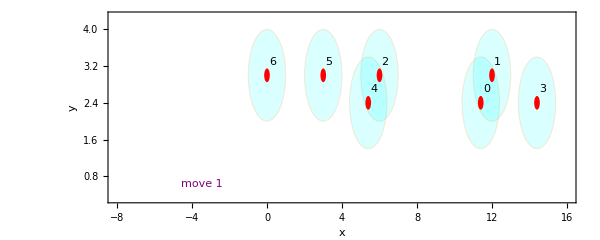

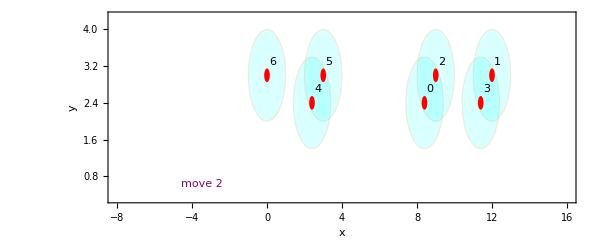

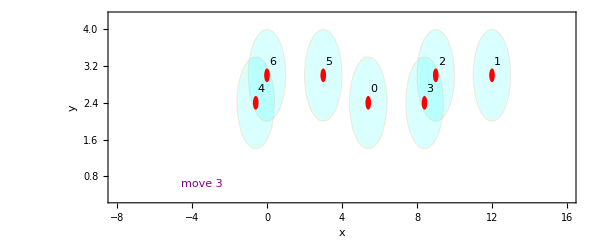

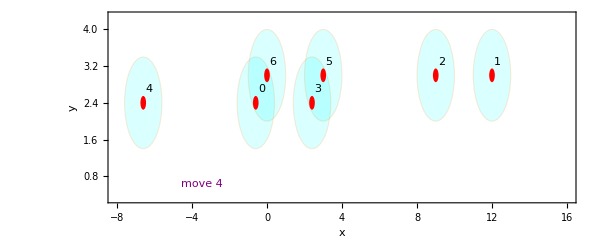

```mathematica
devst=RydbergHub[];
circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{0,3,4}};
circ5={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{1,2,5,6}};
InsertCircuitNoise[circ1,devst];
move1=showst["move 1",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ2,devst];
move2=showst["move 2",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ3,devst];
move3=showst["move 3",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ4,devst];
move4=showst["move 4",{ImagePadding->{{20,18},{18,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
```

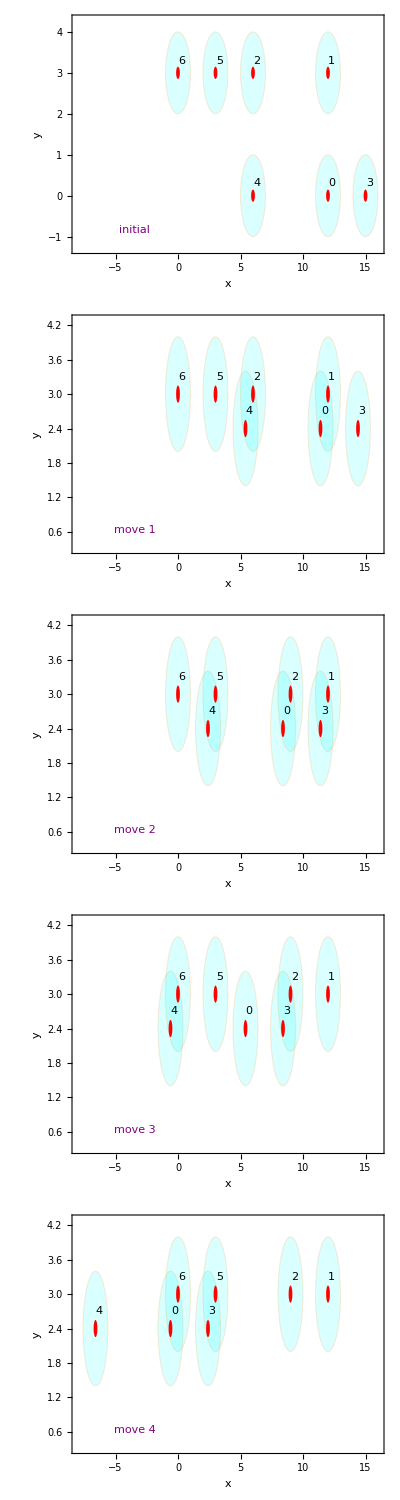

```mathematica
Column[{move0,move1,move2,move3,move4},Spacings->-0.1]
(*Export["rydberg_steane.pdf",%]*)
```

Entire simulation circuit

```mathematica
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];
(* returns indices of the involved stabilizers *)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j
```

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork}=CreateDensityQuregs[7,3];
```

```mathematica
noisycirc=InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[],ReplaceAliases->True];
(*simplify, and remove zero-parameterised operations *)
simpncirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
```

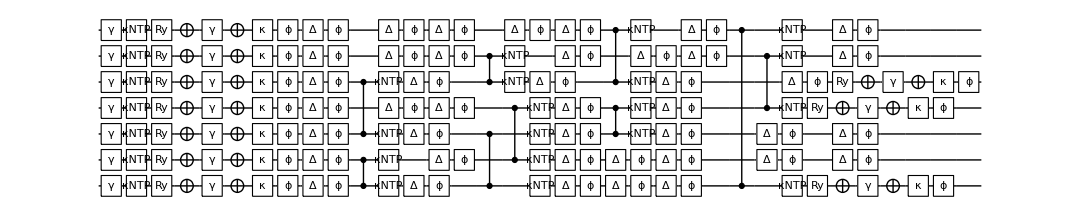

```mathematica
DrawCircuit@simpncirc
```

Logical |+>

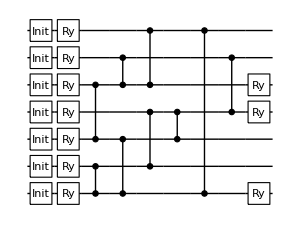

```mathematica
DrawCircuit@DeleteElements[Flatten@Join[circ0,circ1,circ2,circ3,circ4],{Subscript[ShiftLoc, __][_]}]
```

```mathematica
ApplyCircuit[SetQuregMatrix[ρ,IdentityMatrix[2^7]/2^7],simpncirc]
```

{}

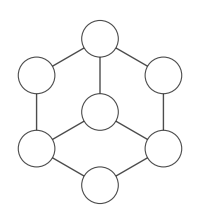

```mathematica
Graph[{2<->4,0<->1,4<->5,2<->0,1<->3,4<->6,2<->3,0<->6,3<->5},
VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{19,FontFamily->"Serif"},ImageSize->200,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],GraphLayout->"TutteEmbedding"]
(*Export["~/vqd/img/graphsteane.pdf",%]*)
```

### Results

#### Modules related to displaying the results

```mathematica
chartSteane[res_,expstabs_,explogic_]:=With[
{
sxcount=res["sxcount"],
szcount=res["szcount"],
nshots=Length@res["outx"],
sxideal=res["sxideal"],
szideal=res["szideal"],
logiccount=res["logiccount"],
logicideal=res["logicideal"],
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]},
size=400
},
Row@{
Show[
		BarChart[
Flatten@{Values@sxcount/nshots,Values@szcount/nshots},ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,5]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->2.5,ChartStyle->Flatten@{ConstantArray[cols[[1]],3],ConstantArray[cols[[2]],3]},
PlotRange->{Automatic,{-0.05,1}},Background->White,ImageSize->{Automatic,size},ImagePadding->{{30,0},{30,10}},BaseStyle->{16,FontFamily->"Serif"}],
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]],
BarChart[Flatten@expstabs,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->5,ChartStyle->cols,PlotRange->{{0.,3},{-0.05,1}},FrameTicks->{Automatic,Automatic},BaseStyle->{16,FontFamily->"Serif"}],
BarChart[explogic,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
Background->White,ImageSize->{Automatic,size},ImagePadding->{{0,0},{30,10}}
]
}
]


(* 
sumarise the result
*)
showResultSteane[res_,expstabs_,explogic_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outx"]//Length},
<|
"nshots"->nshots,
"avgstab"-><|"x"->N@Mean@Values@res["sxcount"]/nshots,"z"->N@Mean@Values@res["szcount"]/nshots,"xl"->N[res["logiccount"]["x"]/nshots],"zl"->N[res["logiccount"]["z"]/nshots]|>,
"errmaxstab"-><|"x"->N@Max[Abs[res["sxcount"]/nshots-First/@First@expstabs]],"z"->N@Max[Abs[res["szcount"]/nshots-First/@Last@expstabs]]|>,
"erravgstab"-><|"x"->N@Mean[Abs[Values@res["sxcount"]/nshots-First@expstabs]],"z"->N@Mean[Abs[Values@res["szcount"]/nshots-Last@expstabs]]|>,
"benchmarkstab"-><|"x"->Table[Between[res[["sxcount"]][j-1]/nshots,Sort[First[expstabs][[j]][[1]]+{1,-1}*First[expstabs][[j]][[2]]]],{j,Length@First@expstabs}],"z"->Table[Between[res[["szcount"]][j-1]/nshots,Sort[Last[expstabs][[j]][[1]]+{1,-1}*Last[expstabs][[j]][[2]]]],{j,Length@Last@expstabs}]|>,
"benchmarklogic"-><|"x"->Between[res[["logiccount"]]["x"]/nshots,Sort[explogic[[1]][[1]]+{1,-1}*explogic[[1]][[2]]]],
"z"->Between[res[["logiccount"]]["z"]/nshots,Sort[explogic[[2]][[1]]+{1,-1}*explogic[[2]][[2]]]]|>,
"errlogic"-><|"x"->Abs[res["logiccount"]["x"]/nshots-First@explogic],"z"->Abs[res["logiccount"]["z"]/nshots-Last@explogic]|>,
"idealavg"-><|"x"->Mean@res["sxideal"],"z"->Mean@res["szideal"],"xl"->res["logicideal"]["x"],"zl"->res["logicideal"]["z"]|>,
"chart"->chartSteane[res,expstabs,explogic]
|>
]
```

#### Quoted from the paper to compare

-Graphics-

```mathematica
steanemean={0.5246212121212122,0.4924242424242424,0.5170454545454546,0.7329545454545454,0.7045454545454546,0.7462121212121211};
steaneminus={0.5,0.46780303030303033,0.4905303030303031,0.7121212121212122,0.6799242424242425,0.7234848484848485};
steaneplus={0.5454545454545455,0.5151515151515151,0.5378787878787878,0.7518939393939393,0.7234848484848485,0.7651515151515151};
```

```mathematica
lsteanemean={0.7134502923976608,-0.015594541910331362};
lsteaneminus={0.6939571150097467,-0.050682261208577};
lsteaneplus={0.7290448343079922,0.009746588693957212};
```

```mathematica
steane=Partition[Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{steanemean,steaneminus,steaneplus}],3]
lsteane=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{lsteanemean,lsteaneminus,lsteaneplus}]
```

{{0.5250.0250.021,0.4920.0250.023,0.5170.0270.021},{0.7330.0210.019,0.7050.0250.019,0.7460.0230.019}}

{0.7130.0190.016,-0.0160.0350.025}

```mathematica
(*stabsteane={{0.52,0.49,0.51},{0.732,0.7,0.75}};*)
logsteane={0.71,-0.02};
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]};
```

#### Results from simulation

```mathematica
steane7<<"supplement/GraphStatesonRydbergHub/steane7.mx";
```

```mathematica
steane7//Length
```

216

```mathematica
truth = Table[
      out = Values@showResultSteane[res, steane, lsteane][[{"benchmarkstab", "benchmarklogic"}]];
      Flatten@{Values@out[[1]], Values@out[[2]]}
      , {res, steane7}];
 
truecount = Count[#, True] & /@ truth;
Max@truecount
```

7

### Take the best result

```mathematica
best = Flatten@Position[truecount, x_ /; x >= 7]
```

{28,70,80,84,86,96,98,102,103,105,115,128,142,144,148,150,156,160,163,168,170,173,177,181,189,201,205,212,216}

```mathematica
bestres=showResultSteane[steane7[[#]], steane, lsteane]&/@best;
```

```mathematica
(* minimum by the distance to the average given in the experiment *)
Ordering[Total@Abs[#-{0.51,0.73,0.71,-0.02}]&/@Flatten[Values/@Values/@bestres[[All,{"avgstab"}]],1],3]
```

{2,18,21}

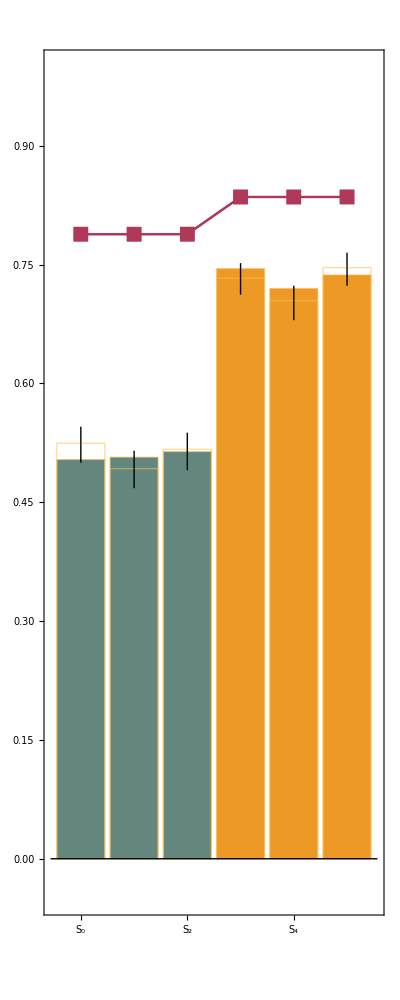
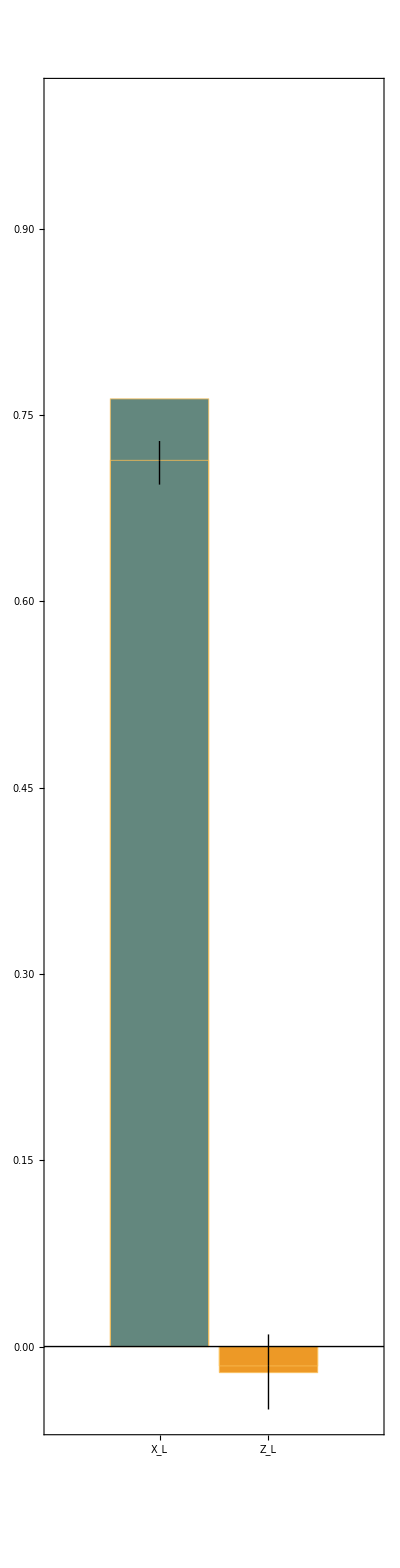
<|nshots→2000,avgstab→<|x→0.508333,z→0.734,xl→0.763,zl→-0.021|>,errmaxstab→<|x→0.0215758,z→0.0404545|>,erravgstab→<|x→0.0130.0150.012,z→0.0120.0130.011|>,benchmarkstab→<|x→{True,True,True},z→{True,True,True}|>,benchmarklogic→<|x→False,z→True|>,errlogic→<|x→0.0500.0190.016,z→0.0050.0350.025|>,idealavg→<|x→0.788493,z→0.835445,xl→0.835995,zl→-0.0000278615|>,chart→-Graphics--Graphics-|>

```mathematica
(* the result shown in the paper *)
bestres[[18]]
```

```mathematica
(*Export["stab_steane.pdf",bestres[[18]][["chart"]]]*)
```